```mathematica
ClearAll["Global'*"]
U={U1,0,0};X={x,y,z};
r=√(x^2+y^2+z^2);
(*Stokes flow velocity and pressure field for a sphere of radius a translating with velocity U*)
```

```mathematica
u=(3a)/4(U/r+((U.X)X)/r^3)+a^3/4(U/r^3-(3(U.X)X)/r^5);
p=(3μ a)/2(U.X)/r^3
(*Stokeslet Velocity Field*)
Subscript[U, s]=(3a)/4(U/r+((U.X)X)/r^3);
(*Components of the velocity field*)
ux=u⟦1⟧;uy=u⟦2⟧;uz=u⟦3⟧;
Subscript[U, sx]=Subscript[U, s]⟦1⟧;Subscript[U, sy]=Subscript[U, s]⟦2⟧;Subscript[U, sz]=Subscript[U, s]⟦3⟧;
u//MatrixForm
Subscript[U, s]//MatrixForm
```

(3 a U1 x μ)/(2 (x^2+y^2+z^2)^(3/2))

(1/4 a^3 (-(3 U1 x^2)/((x^2+y^2+z^2)^(5/2))+U1/((x^2+y^2+z^2)^(3/2)))+3/4 a ((U1 x^2)/((x^2+y^2+z^2)^(3/2))+U1/(√(x^2+y^2+z^2)))
-(3 a^3 U1 x y)/(4 (x^2+y^2+z^2)^(5/2))+(3 a U1 x y)/(4 (x^2+y^2+z^2)^(3/2))
-(3 a^3 U1 x z)/(4 (x^2+y^2+z^2)^(5/2))+(3 a U1 x z)/(4 (x^2+y^2+z^2)^(3/2)))

(3/4 a ((U1 x^2)/((x^2+y^2+z^2)^(3/2))+U1/(√(x^2+y^2+z^2)))
(3 a U1 x y)/(4 (x^2+y^2+z^2)^(3/2))
(3 a U1 x z)/(4 (x^2+y^2+z^2)^(3/2)))

```mathematica
(*Stress field*)σ=-p IdentityMatrix[3]+μ ((∇_{x,y,z} u)+Transpose[∇_{x,y,z} u]);
```

```mathematica
(*Surface stress*)σs= FullSimplify[(σ/.{x->a Sin[θ]Cos[ϕ],y->a Sin[θ]Sin[ϕ],z->a Cos[θ]}),Assumptions-> {Im[a]==0,Re[a]>0}]
```

{{(9 U1 μ Cos[ϕ] (-3+Cos[2 ϕ]) Sin[θ]-6 U1 μ Cos[ϕ]^3 Sin[3 θ])/(8 a),(-3 U1 μ (3+Cos[2 θ]) Sin[θ] Sin[ϕ]+6 U1 μ Sin[θ]^3 Sin[3 ϕ])/(8 a),(3 U1 μ Cos[θ]^3 (-1+Cos[2 ϕ] Tan[θ]^2))/(2 a)},{(-3 U1 μ (3+Cos[2 θ]) Sin[θ] Sin[ϕ]+6 U1 μ Sin[θ]^3 Sin[3 ϕ])/(8 a),-(3 U1 μ (3 Cos[3 ϕ] Sin[θ]+Cos[ϕ] (5 Sin[θ]+4 Sin[3 θ] Sin[ϕ]^2)))/(16 a),(3 U1 μ Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/a},{(3 U1 μ Cos[θ]^3 (-1+Cos[2 ϕ] Tan[θ]^2))/(2 a),(3 U1 μ Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[ϕ])/a,(3 U1 μ Cos[ϕ] (-Sin[θ]+Sin[3 θ]))/(4 a)}}

```mathematica
(*We need coordinate transformation from cartesian coordinate to spherical because the INTEGRAL will be over a spherical body.*)
```

```mathematica
(*Unit normal*)n={Sin[θ] Cos[ϕ],Sin[θ]Sin[ϕ], Cos[θ]};
(*Unit Normal are always in cartesian coordinates*)
```

```mathematica
(*Surface force density,or traction.Note that it is independent of angular position*)
fs=FullSimplify[σs.n]
(*Viscous drag on the sphere*)
F=∫_0^(2π) ∫_0^π fs Sin[θ] a^2 ⅆθⅆϕ
```

{-(3 U1 μ)/(2 a),0,0}

{-6 a π U1 μ,0,0}

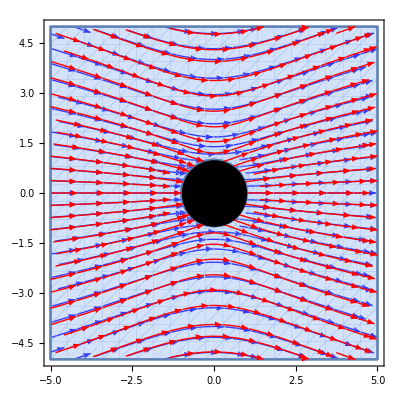

```mathematica
xm=5;
zm=5;
a0=1;
U0=1;
uxp=(ux/.{U1->U0,a->a0});
uyp=(uy/.{U1->U0,a->a0});
uzp=(uz/.{U1->U0,a->a0});
Subscript[U, sxp]=(Subscript[U, sx]/.{U1->U0,a->a0});
Subscript[U, syp]=(Subscript[U, sy]/.{U1->U0,a->a0});
Subscript[U, szp]=(Subscript[U, sz]/.{U1->U0,a->a0});
P2=Graphics[Disk[{0,0},a0]];
P11=StreamPlot[{{Subscript[U, sxp]/.{y->0},Subscript[U, szp]/.{y->0}}},{x,-xm,xm},{z,-zm,zm},RegionFunction->((a0^2<#1^2+#2^2<xm^2+zm^2)&),StreamColorFunction->(Red&),PlotLegends->{"Stokeslet"}];
P1= StreamPlot[{{uxp/.{y->0},uzp/.{y->0}}},{x,-xm,xm},{z,-zm,zm},RegionFunction->((a0^2<#1^2+#2^2<xm^2+zm^2)&),StreamColorFunction->(Blue&),PlotLegends->{"Full"}];
Show[P1,P11,P2]
```

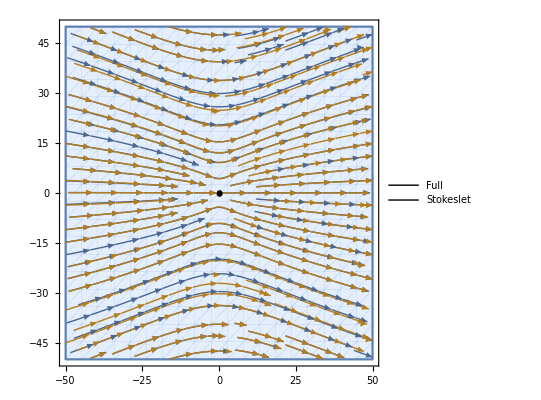

```mathematica
xm=50;
zm=50;
a0=1;
U0=1;
uxp=(ux/.{U1->U0,a->a0});
uyp=(uy/.{U1->U0,a->a0});
uzp=(uz/.{U1->U0,a->a0});
Subscript[U, sxp]=(Subscript[U, sx]/.{U1->U0,a->a0});
Subscript[U, syp]=(Subscript[U, sy]/.{U1->U0,a->a0});
Subscript[U, szp]=(Subscript[U, sz]/.{U1->U0,a->a0});
P2=Graphics[Disk[{0,0},a0]];
P1= StreamPlot[{{uxp/.{y->0},uzp/.{y->0}},{Subscript[U, sxp]/.{y->0},Subscript[U, szp]/.{y->0}}},{x,-xm,xm},{z,-zm,zm},RegionFunction->((#1^2+#2^2>a0^2)&),StreamColorFunction->(Green& Blue),PlotLegends->{"Full","Stokeslet"}];
Show[P1,P2]
```